```mathematica
(*These functions are to precompute the time integrals*)
(*Compute the partitions of the list x*)
partition[{x_}]:={{{x}}};
partition[{r__,x_}]:=Join@@(ReplaceList[#,{{b___,{S__},a___}:>{b,{S,x},a},{S__}:>{S,{x}}}]&/@partition[{r}]);
(*Kimura's eigenvalues*)
KimuraEig[i_]:=1/2*i*(i+1);
(*The integrand of all the time integrals*)
integrand[k_]:=Exp[Sum[( KimuraEig[q[i+1]] - KimuraEig[q[i]] - (2^(1+r[i])* Ne * VG / W))s[i],{i,1,k}]];
(*The limits of the time integrals*)
sLimits[k_]:= Join[{{s[k],0,t}},Reverse[Table[{s[j],0,s[j+1]},{j,1,k-1}]]];
(*Define the limits of the k fold sum over the j_i s *)
rLimits[k_] := Table[{r[i],0,1},{i,1,k}];
(*Define the limits of the k+1 fold infinite sums. Truncating after n_ terms*)
qLimits[k_, n_ ] := Join[{{q[1],1,n}},Table[{q[j],q[j-1]-2,q[j-1]+2,1},{j,2,k+1}]];
(*Compute the appropriat integrand for the partition*)
integrandPart[myPartition_,k_]:=Module[{curFun,firstElement,block,curElement},
curFun = integrand[k];
 For[a=1,a≤Length[myPartition],a++,
firstElement = myPartition[[a,1]];
For[b=2,b≤Length[myPartition[[a]]],b++,
curElement = myPartition[[a,b]];
curFun = curFun/.q[curElement]->q[firstElement];
];
];
curFun//FullSimplify
]
computeInts[k_]:=Module[{curParts,curLimits,curIntegrand,curInts,j},
curParts = partition[Table[j,{j,1,k+1}]];
curLimits = sLimits[k];
For[j=1,j≤Length[curParts],j++,
curIntegrand=integrandPart[curParts[[j]],k];
curInts[curParts[[j]]]=Integrate[curIntegrand,Evaluate[Sequence@@curLimits]];
];
Return[curInts]
]
```

```mathematica
qLimits[3,10]
rLimits[3]
```

{{q[1],1,10},{q[2],-2+q[1],2+q[1],1},{q[3],-2+q[2],2+q[2],1},{q[4],-2+q[3],2+q[3],1}}

{{r[1],0,1},{r[2],0,1},{r[3],0,1}}

```mathematica
Join[qLimits[3,10],rLimits[3]]
```

{{q[1],1,10},{q[2],-2+q[1],2+q[1],1},{q[3],-2+q[2],2+q[2],1},{q[4],-2+q[3],2+q[3],1},{r[1],0,1},{r[2],0,1},{r[3],0,1}}

```mathematica
(*These functions are to compute the Gegenbauer integrals*)
(*The normalizations for the Gegenbauer polynomials*)
gegenbauerNorm[i_,λ_:3/2] := π*2^(1-2*λ)*Gamma[i+2*λ]/(Factorial[i]*(i+λ)*Gamma[λ]^2);
(*Define Int_{0^1}x^2(1-x)^(1+j)C_{i-1}^{(3/2)}(1-2*x)C_{j-1}^{(3/2)}(1-2*x)dx*)
f[0,0]=1;
f[a_,b_]:=a^b
gegenbauerInt[a_,b_,r_]:=2^(-(4+r))*(KroneckerDelta[a,b]* gegenbauerNorm[a] - 
(f[(1/(3+2a) * 
((a+1)*KroneckerDelta[a,b-1]*gegenbauerNorm[a+1]+
(a+2)*KroneckerDelta[a,b+1]*gegenbauerNorm[a-1])),(1-r) ] * (*3rdd to last partenthesis on this line was missing. check if this fixed*)
f[(1/((2*a+3)*(2*b+3))*
((a+1)*(b+1)*KroneckerDelta[a,b]*gegenbauerNorm[a+1]+
(a+1)*(b+2)*KroneckerDelta[a,b-2]*gegenbauerNorm[a+1]+
(a+2)*(b+1)*KroneckerDelta[a,b+2]*gegenbauerNorm[a-1]+
(a+2)*(b+2)*KroneckerDelta[a,b]*gegenbauerNorm[a-1])),r]));
```

```mathematica
(*Functions to compute the path integral to order k*)
(*Find the partition given the current state of the summation*)
findEquiv[vals_] := Module[{tempPart},
tempPart=Function[val,Flatten[Position[vals,val]]]/@Union[vals];
Sort[tempPart,Less[First[#1],First[#2]]&]
]
(*Define the coefficients from Kimura's solution*)
kimuraCoefficient[i_]:= If[i>0,(2*i+1)/(i*(i+1)),0];
(*Kimura's transition density*)
(*TODO get rid of the default*)
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
(*Compute the path integral at order k*)
pathInt[x_,y_,t_,k_,n_, Ne_, α_, Λ_, W_,VG_]:= Module[{qlims, rlims, lims, tInts},
(*myInds = Table[{i[j],1,n},{j,1,k+1}];*)
qlims = qLimits[k,n];
rlims = rLimits[k];
lims = Join[qlims,rlims];
tInts = computeInts[k];
4 *(8 Ne^2 α Λ / W^2)^k * x*(1-x)*ParallelSum[If[Negative@Min@Table[q[j],{j,1,k+1}],0,
Product[kimuraCoefficient[q[j]],{j,1,k+1}]*
Exp[-KimuraEig[q[k+1]]*t]*
GegenbauerC[q[1]-1,3/2,1-2*x]*
GegenbauerC[q[k+1]-1,3/2,1-2*y]*
Product[(2VG)^(1-r[j]) (- α Λ)^r[j] gegenbauerInt[q[j]-1,q[j+1]-1, r[j]],{j,1,k}]*
tInts[findEquiv[Table[q[j],{j,1,k+1}]]]],Evaluate[Sequence@@lims]]];
```

```mathematica
pathIntLog[x_,y_,t_,k_,n_, Ne_, α_, Λ_, W_,VG_]:= Module[{qlims, rlims, lims, tInts},
(*myInds = Table[{i[j],1,n},{j,1,k+1}];*)
qlims = qLimits[k,n];
rlims = rLimits[k];
lims = Join[qlims,rlims];
tInts = computeInts[k];
4 *(8 Ne^2 α Λ / W^2)^k * x*(1-x)*ParallelSum[If[Negative@Min@Table[q[j],{j,1,k+1}],0,
Product[kimuraCoefficient[q[j]],{j,1,k+1}]*
Exp[(-KimuraEig[q[k+1]]*t)+
Log[GegenbauerC[q[1]-1,3/2,1-2*x]]+
Log[GegenbauerC[q[k+1]-1,3/2,1-2*y]]]*
Product[(2VG)^(1-r[j]) (- α Λ)^r[j] gegenbauerInt[q[j]-1,q[j+1]-1, r[j]],{j,1,k}]*
tInts[findEquiv[Table[q[j],{j,1,k+1}]]]],Evaluate[Sequence@@lims]]];
```

```mathematica
(*TODO find out if we need to do the find Equiv thing or not. It'd make a difference for VG = 0 but only if that is declared prior to the integrand being calculated*)
```

```mathematica
o[0] = Kimura[x,y,t,10];
```

```mathematica
o[1] = pathInt[x,y,t,1,10, Ne, α, Λ, W,VG];
```

```mathematica
o[2] = SetPrecision[pathInt[x,y,t,2,10, Ne, α, Λ, W,VG],100];
```

```mathematica
o[3] = SetPrecision[pathInt[x,y,t,3,10, Ne, α, Λ, W,VG],50];
```

```mathematica
(*o[4] = pathInt[x,y,t,4,10, Ne, α, Λ, W,VG];*)
```

```mathematica
olog[1]=pathInt[x,y,t,1,10, Ne, α, Λ, W,VG];
```

```mathematica
olog[2]=pathInt[x,y,t,2,10, Ne, α, Λ, W,VG];
```

```mathematica
(*o[5] = pathInt[x,y,t,5,10, Ne, α, Λ, W,VG]*)
```

$Aborted

```mathematica
(*Save["o1through4.m",o]*)
(*Get["o1through4.m"]*)
```

```mathematica
o[0]/.{x->.2,y->.4,t->.2}
```

0.937609

```mathematica
o[1]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

0.94163

```mathematica
o[2]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: 1/(«122»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(«122»)^801. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.473746

```mathematica
NumberForm[0.47374633293160123,16]
```

0.4737463329316013

```mathematica
o[3]
```

```mathematica
o[3]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.15526

```mathematica
NumberForm[0.15525975186138727,16]
```

0.1552597518613873

```mathematica
o[4]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-5.16496×10^-14

```mathematica
(*newversion = (2 Ne^2 α Λ / W^2)^2 * o[2]*)
```

```mathematica
(*DumpSave["newversion.mx",newversion]*)
For[k = 0, k ≤3,k++,
approx[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[ o[j], {j, 0, k}]
]
```

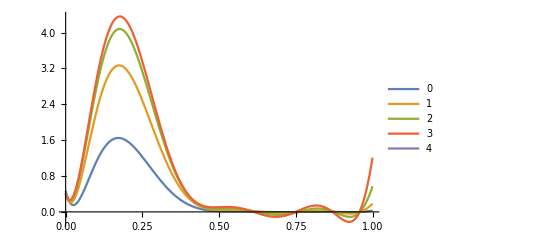

```mathematica
Plot[Evaluate[Table[approx[k]/. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1},{k,0, 4}]],{y,0,1},PlotLegends->{Table[k,{k,0,4}]}]
```

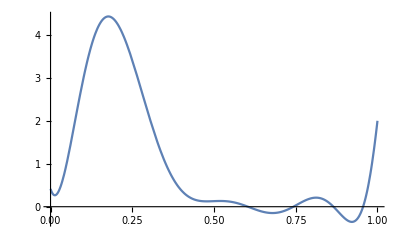

```mathematica
Plot[Evaluate[approx[4] /. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}], {y,0,1}]
```

```mathematica
approx[4] /. {x->0.2, t->0.1,Ne->500,α->0.005, Λ -> 1, W->1, VG->1, y ->0.4}
NIntegrate[approx[4] /.{x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}, {y,0,1}]
```

General::munfl: Exp[-800.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.848427

1.02353

```mathematica
pade = PadeApproximant[approx/.γ^2->g,{g,0,2}]/.g->γ^2;
```

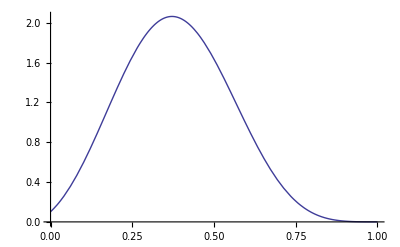

```mathematica
Plot[pade/.{x->.2,t->.1,γ->10},{y,0,1}]
```

```mathematica
vals10 = Table[approx/.{x->.2,t->.1,γ->5},{y,0,1,.05}]
```

{0.364043,0.942617,1.56848,2.1083,2.46219,2.58194,2.47292,2.1829,1.78335,1.34942,0.943708,0.606975,0.356141,0.188323,0.0881546,0.0355679,0.0118655,0.00305193,0.00052951,0.0000446591,1.4838×10^-7}

```mathematica
Export["~/Desktop/testMathematica.txt",vals10]
```

~/Desktop/testMathematica.txt

```mathematica
mass = Table[NIntegrate[approx/.{x->.2,t->.1},{y,0,1}],{γ,-10,10,.5}]
```

{0.917192,0.926483,0.934135,0.940547,0.946018,0.95077,0.954966,0.958726,0.962134,0.965252,0.968123,0.970778,0.973239,0.975523,0.977641,0.979605,0.981423,0.983103,0.984655,0.986084,0.987399,0.988607,0.989714,0.990727,0.991653,0.992497,0.993264,0.993958,0.994579,0.995117,0.995551,0.995833,0.995867,0.99548,0.994365,0.992,0.987512,0.979476,0.965594,0.942217,0.903603}

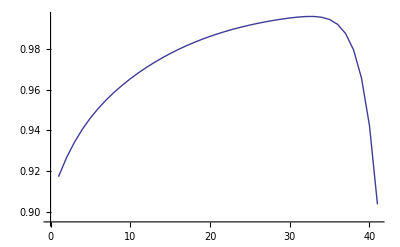

```mathematica
ListLinePlot[mass]
```

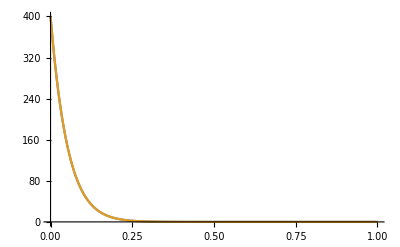

```mathematica
Plot[{D[Kimura[x,y,.1,50],x]/.x->.0,4*Entrance[y,.1,50]},{y,0,1},PlotRange->All]
```

```mathematica
?GegenbauerC
```

GegenbauerC[n,m,x] gives the Gegenbauer polynomial C_n^(m)(x). 
GegenbauerC[n,x] gives the renormalized form lim_(m→0) C_n^(m)(x)/m.

```mathematica
Clear[n]
```

```mathematica
Limit[D[4*x*(1-x)*GegenbauerC[i-1,3/2,1-2*x],x],x->0]//FullSimplify
```

2 i (1+i)

```mathematica
Entrance[y_,t_,n_:20]:=2*Sum[(2*i+1)*GegenbauerC[i-1,3/2,1-2*y]*Exp[-1/2*i*(i+1)*t],{i,1,n}]
```

```mathematica
stuff = Table[NIntegrate[Binomial[5,k]*y^k(1-y)^(5-k)*Entrance[y,.2,50],{y,0,1}],{k,0,5}]
```

{6.75839,2.49488,0.812877,0.222196,0.0461631,0.00562481}

```mathematica
stuff/Total[stuff]
```

{0.412487,0.267168,0.16358,0.0924888,0.0461478,0.0181288}

```mathematica
stuff[[2;;5]]/Total[stuff[[2;;5]]]
```

{0.907103,0.0862273,0.00634792,0.000322154}

```mathematica
Plot[Integrate[Entrance[y,t,50],{y,0,1}],{t,.001,.5},PlotRange->All]
```

-Graphics-

```mathematica
Clear[n]
```

```mathematica
Exp[-800+Log[400.3]]
```

General::munfl: Exp[-794.008] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
SetPrecision[Exp[-800],100]
```

3.667874584177687213455495654260798215469634226612640705069151310903542448310183622525663193492234×10^-348